# Hierarchical Spin-Glasses

## Fixed-point analysis

```mathematica
Clear["Global`*"]
```

```mathematica
FullSimplify[Solve[P==(Sinh[β J]+P^2 Cosh[β J])/(Cosh[β J]+P^2 Sinh[β J]),P]]
```

{{P→1},{P→1/2 (-1+Coth[J β]-√(ⅇ^(J β)) Csch[J β] √((-3+Coth[J β]) Sinh[J β]))},{P→1/2 (-1+Coth[J β]+√(ⅇ^(J β)) Csch[J β] √((-3+Coth[J β]) Sinh[J β]))}}

```mathematica
Pplus[β_]=1/2 (-1+Coth[J β]+√(ⅇ^(J β)) Csch[J β] √((-3+Coth[J β]) Sinh[J β]));
Pminus[β_]=1/2 (-1+Coth[J β]-√(ⅇ^(J β)) Csch[J β] √((-3+Coth[J β]) Sinh[J β]));
```

```mathematica
βc=Log[2]/(2J);
```

### Ferromagnetic Case, J>0

```mathematica
J=1;
```

Study the stability empirically by starting off at some value and iterating.

```mathematica
Clear[k,P,n,Ptrue,line1,plot,ticks,newticks,β,h]
n=500;
β=1/4.;
h=0;
P[0]=1-0.8;
For[k=1,k≤n,k++,
P[k]=(Sinh[β J]+Cosh[β J] P[-1+k]^2)/(Cosh[β J]+Sinh[β J] P[-1+k]^2);
];
Clear[k]
```

```mathematica
P[n]
```

0.368377

```mathematica
{Pminus[β],Pplus[β],1}
```

{0.368377,2.71461,1}

Stability around P^(0): solution is stable for β>β_c

```mathematica
Clear[β,P]
P=1+δ;
```

```mathematica
FullSimplify[Series[(Sinh[β J]+Cosh[β J] P^2)/(Sinh[β J] P^2+Cosh[β J])-P,{δ,0,1}]]
```

(-1+2 ⅇ^(-2 β)) δ+O[δ]^2

```mathematica
Assuming[β∈Reals,FullSimplify[Solve[Normal[%]==0,β]]]
```

{{β→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[2]), C[1]∈ℤ]}}

Stability around P^(-): solution is stable for β<β_c

```mathematica
Clear[β,P]
P=Pminus[β]+δ
```

δ+1/2 (-1+Coth[β]-√(ⅇ^β) Csch[β] √((-3+Coth[β]) Sinh[β]))

```mathematica
FullSimplify[Series[(Sinh[β J]+Cosh[β J] P^2)/(Sinh[β J] P^2+Cosh[β J])-P,{δ,0,1}]]
```

(-2+ⅇ^(2 β)) δ+O[δ]^2

```mathematica
Assuming[β∈Reals,FullSimplify[Solve[Normal[%]==0,β]]]
```

{{β→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[2]), C[1]∈ℤ]}}

Stability around P^(+): solution is stable for β<β_c

```mathematica
Clear[β,P]
P=Pplus[β]+δ
```

δ+1/2 (-1+Coth[β]+√(ⅇ^β) Csch[β] √((-3+Coth[β]) Sinh[β]))

```mathematica
FullSimplify[Series[(Sinh[β J]+Cosh[β J] P^2)/(Sinh[β J] P^2+Cosh[β J])-P,{δ,0,1}]]
```

(-2+ⅇ^(2 β)) δ+O[δ]^2

```mathematica
Assuming[β∈Reals,FullSimplify[Solve[Normal[%]==0,β]]]
```

{{β→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[2]), C[1]∈ℤ]}}

Expand P^(-) around the critical point

```mathematica
FullSimplify[Series[Pminus[β],{β,βc,1}]]
```

1-(2 (√2 √(-2 β+Log[2])) √(β-Log[2]/2))/(√(2 β-Log[2]))-4 (β-Log[2]/2)+O[β-Log[2]/2]^(3/2)

### Anti-Ferromagnetic Case, J<0

```mathematica
J=-1;
```

Study the stability empirically by starting off at some value and iterating.

```mathematica
Clear[k,P,n,Ptrue,line1,plot,ticks,newticks,β,h]
n=500;
β=1/4.;
h=0;
P[0]=1-0.8;
For[k=1,k≤n,k++,
P[k]=(Sinh[β J]+Cosh[β J] P[-1+k]^2)/(Cosh[β J]+Sinh[β J] P[-1+k]^2);
];
Clear[k]
```

```mathematica
P[n]
```

-0.205003

```mathematica
{Pminus[β],Pplus[β],1}
```

{-0.205003,-4.87799,1}

Stability around P^(0): solution is unstable for all β

```mathematica
Clear[β,P]
P=1+δ;
```

```mathematica
FullSimplify[Series[(Sinh[β J]+Cosh[β J] P^2)/(Sinh[β J] P^2+Cosh[β J])-P,{δ,0,1}]]
```

(-1+2 ⅇ^(2 β)) δ+O[δ]^2

Stability around P^(-): solution is stable for all β

```mathematica
Clear[β,P]
P=Pminus[β]+δ
```

δ+1/2 (-1-Coth[β]+√(ⅇ^-β) Csch[β] √(-(-3-Coth[β]) Sinh[β]))

```mathematica
FullSimplify[Series[(Sinh[β J]+Cosh[β J] P^2)/(Sinh[β J] P^2+Cosh[β J])-P,{δ,0,1}]]
```

(-2+ⅇ^(-2 β)) δ+O[δ]^2

Stability around P^(+): solution is stable for all β

```mathematica
Clear[β,P]
P=Pplus[β]+δ
```

δ+1/2 (-1-Coth[β]-√(ⅇ^-β) Csch[β] √(-(-3-Coth[β]) Sinh[β]))

```mathematica
FullSimplify[Series[(Sinh[β J]+Cosh[β J] P^2)/(Sinh[β J] P^2+Cosh[β J])-P,{δ,0,1}]]
```

(-2+ⅇ^(-2 β)) δ+O[δ]^2

## Junk

```mathematica
Y[n-1,1]=(Sinh[β J[n-1,1]]+Cosh[β J[n-1,1]]Y[n-2,1]Y[n-2,2])/(Cosh[β J[n-1,1]]+Sinh[β J[n-1,1]]Y[n-2,1]Y[n-2,2])
```

(Sinh[β J[-1+n,1]]+Cosh[β J[-1+n,1]] Y[-2+n,1] Y[-2+n,2])/(Cosh[β J[-1+n,1]]+Sinh[β J[-1+n,1]] Y[-2+n,1] Y[-2+n,2])

```mathematica
x=Y+FullSimplify[(β^-1 D[Log[Cosh[β J[n,1]]+Sinh[β J[n,1]]Y[n-1,1]Y[n-1,2]], J[n-1,1]])/.J[k_,p_]:>J/.Y[k_,p_]:>Y]
```

Y-(2 Y (-1+Y^4) Sinh[J β])/((Cosh[J β]+Y^2 Sinh[J β]) (1-Y+(1+Y) (Cosh[2 J β]+Y^2 Sinh[2 J β])))

```mathematica
x/.Y->1
```

1

```mathematica
βc=Log[2]/2;J=1;
```

```mathematica
FullSimplify[Series[x/.Y->1-ϵ √(β-βc),{β,βc,1}]]
```

1-1/2 ϵ √(β-Log[2]/2)-1/2 ϵ^2 (β-Log[2]/2)+O[β-Log[2]/2]^(3/2)

```mathematica
H[n_]=Sum[Sum[-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-k)}],{k,0,n}];
HLeftChild[n_]=Sum[Sum[-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-1-k)}],{k,0,n-1}];
HRightChild[n_]=Sum[Sum[-J[k,2^(n-k-1)+p]Product[s[i+2^(n-1)],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-1-k)}],{k,0,n-1}];;
```

check:

```mathematica
Table[Simplify[H[n]-(HLeftChild[n]+HRightChild[n]-J[n,1]Product[s[i],{i,1,2^n}])],{n,3,10}]
```

{0,0,0,0,0,0,0,0}

## General Couplings

### General Case

```mathematica
Clear["Global`*"]
```

Introduce the Hamiltonian of the (k,p) sub-system:

```mathematica
H[0,p_]=-J[0,p]s[p];
H[k_,p_]:=H[k-1,2p-1]+H[k-1,2p]-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}];
```

Pick a value of n:

```mathematica
n=4;
Nn=2^n;
Print["number of spins N = ", 2^n];
Print["number of states 2^N = ", 2^Nn];
```

number of spins N = 16

number of states 2^N = 65536

Compute the partition function for general couplings and temperature using the recursion:

```mathematica
Clear[Z,Y]
Do[Z[0,p]=2Cosh[β J[0,p]],{p,1,2^n}];
Do[Y[0,p]=Tanh[β J[0,p]],{p,1,2^n}];
For[k=1,k≤n,k++,
For[p=1,p≤2^n,p++,
Z[k,p]=Z[k-1,2p-1]Z[k-1,2p](Cosh[β J[k,p]]+Sinh[β J[k,p]]Y[k-1,2p-1]Y[k-1,2p]);
Y[k,p]=β^-1 D[Log[Z[k,p]], J[k,p]];
];];
```

Pick a random draw of the interactions, letting the standard deviation be a function of tree height:

```mathematica
σ[kk_]=1;
Couplings=Table[RandomVariate[NormalDistribution[1,0.001σ[k]]],{k,0,n},{p,1,2^(n-k)}];

Couplings=Table[2RandomVariate[BernoulliDistribution[0.5]]-1,{k,0,n},{p,1,2^(n-k)}];

CouplingRules=Flatten[Table[J[k,p]->Couplings[[k+1,p]],{k,0,n},{p,1,2^(n-k)}]];
HH=H[n,1]/.CouplingRules;
```

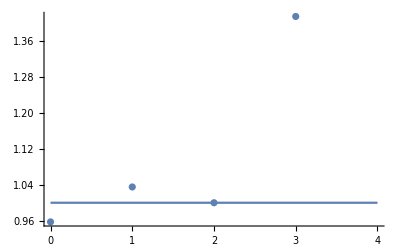

```mathematica
Show[{Plot[σ[k],{k,0,n}],ListPlot[Table[{k,Sqrt[Variance[Couplings[[k+1]]]]},{k,0,n-1}]]},PlotRange->All]
```

Compute the ground state of a sub-system by brute force:

```mathematica
GroundStateBrute[k_,p_]:=
Module[{gs,spinlist,states,Enlist},
spinlist=Table[s[i],{i,1+(p-1)2^k,p 2^k}];
states=Flatten[Outer[List,##]&@@Table[{-1,1},{2^k}],2^k-1];
Enlist = {};
For[i=1,i≤2^(2^k),i++,
AppendTo[Enlist,H[k,p]/.CouplingRules/.Table[spinlist[[j]]->states[[i,j]],{j,1,2^k}]];
];
gs=states[[Position[Enlist,Min[Enlist]][[1,1]]]];
gs]
```

Compute the ground state of a sub-system using the recursive property. This is the most efficient version of the algorithm, where I only consider O(1) new states at each iteration.

```mathematica
listProduct[x_List]:=Times@@x
```

```mathematica
GroundStateNew[k_,p_]:=
Module[{spinlist,state0,state1,statesA,statesB,state00,state01,state10,En00,En01,En10,stateList,EnList,sortedpairs},
spinlist=Table[s[i],{i,1+(p-1)2^k,p 2^k}];
If[k==0,
state0={Sign[J[k,p]/.CouplingRules]};
state1={-Sign[J[k,p]/.CouplingRules]};
];
If[k>0,
(* get the 00, 01, and 10 states *)
statesA=GroundStateNew[k-1,2p-1];
statesB=GroundStateNew[k-1,2p];
state00=Join[statesA[[1]],statesB[[1]]];
state01=Join[statesA[[1]],statesB[[2]]];
state10=Join[statesA[[2]],statesB[[1]]];
En00=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state00[[j]],{j,1,2^k}];
En01=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state01[[j]],{j,1,2^k}];
En10=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state10[[j]],{j,1,2^k}];
(* compile a sorted list of states and energies *)
stateList={state00,state01,state10};
EnList={En00,En01,En10};
sortedpairs = SortBy[Transpose[{EnList,stateList}],First];
EnList=Table[sortedpairs[[i,1]],{i,1,3}];
stateList=Table[sortedpairs[[i,2]],{i,1,3}];
state0=stateList[[1]];
If[listProduct[stateList[[2]]]==-listProduct[state0],state1=stateList[[2]];,state1=stateList[[3]];];
];
(* return the lowest and second-lowest energy state *)
{state0,state1}]
```

Compute the ground state of a sub-system using the recursive property. This is a less efficient version of the algorithm. At step k I consider all 2^k states which are 1 spin-flip away from my current state.

```mathematica
GroundState[k_,p_]:=
Module[{state0,state,En,EnTemp,stateTemp,spinlist},
spinlist=Table[s[i],{i,1+(p-1)2^k,p 2^k}];
If[k==0,state={Sign[J[k,p]/.CouplingRules]};];
If[k>0,
state0=Join[GroundState[k-1,2p-1],GroundState[k-1,2p]];
state=state0;
En=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state[[j]],{j,1,2^k}];
For[i=1,i≤2^k,i++,
stateTemp=state0;
stateTemp[[i]]=-stateTemp[[i]];
EnTemp=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->stateTemp[[j]],{j,1,2^k}];
If[EnTemp<En,state=stateTemp;En=EnTemp];
];
];
state]
```

Check that these all agree:

```mathematica
Table[GroundState[k,p]==GroundStateNew[k,p][[1]],{k,0,n},{p,1,2^(n-k)}]
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,False,False,False,False,True},{True,True,True,False},{True,False},{False}}

```mathematica
Table[GroundState[k,p]==GroundStateBrute[k,p],{k,0,n},{p,1,2^(n-k)}]
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,False,False,False,False,True},{True,True,True,False},{True,False},{False}}

introduce a function that tests whether a configuration is a local minima:

```mathematica
LocalMinQ[spins_]:=
Module[{localMin=True},
E1=HH/.Table[s[j]->spins[[j]],{j,1,2^n}];
p=1;
While[p≤2^n&&localMin==True,
spinstmp=spins;
spinstmp[[p]]=-spinstmp[[p]];
E2=HH/.Table[s[j]->spinstmp[[j]],{j,1,2^n}];
If[E2<E1,localMin=False;];
p+=1;
];
localMin]
```

compute the partition function, spectrum, and number of local minima by brute-force:

```mathematica
states=Flatten[Outer[List,##]&@@Table[{-1,1},{Nn}],Nn-1];
```

```mathematica
partitionFunc=0;
Enlist = {};
Enlist0={};
Maglist={};
LocalMinima={};
For[i=1,i≤2^Nn,i++,
AppendTo[Enlist0,H[n]/.Table[s[j]->states[[i,j]],{j,1,2^n}]];
AppendTo[Enlist,HH/.Table[s[j]->states[[i,j]],{j,1,2^n}]];
AppendTo[Maglist,Total[states[[i]]]];
If[LocalMinQ[states[[i]]],AppendTo[LocalMinima,states[[i]]]];
partitionFunc+=Exp[-HH]/.Table[s[j]->states[[i,j]],{j,1,2^n}];
];
Clear[i]
```

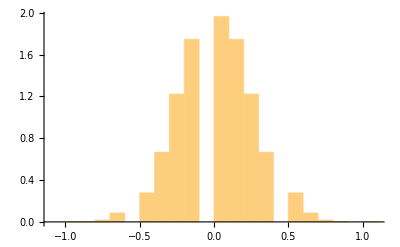

```mathematica
Histogram[(Maglist/2^n//N),40,"ProbabilityDensity"]
```

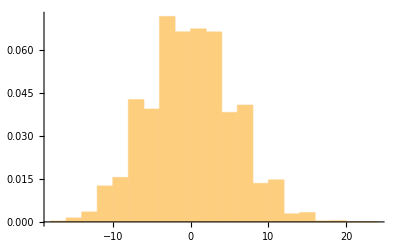

```mathematica
Histogram[Enlist,40,"ProbabilityDensity"]
```

sort the states by energy:

```mathematica
sortedpairs = SortBy[Transpose[{Enlist,states}],First];
Enlist=Table[sortedpairs[[i,1]],{i,1,2^Nn}];
states=Table[sortedpairs[[i,2]],{i,1,2^Nn}];
```

Examine the ground state:

```mathematica
gs=GroundState[n,1];
```

```mathematica
gs==states[[1]]
```

False

Ground state energy and degeneracy

```mathematica
Tally[Enlist]
```

{{-17,40},{-15,182},{-13,456},{-11,1642},{-9,2029},{-7,5584},{-5,5152},{-3,9376},{-1,8676},{1,8812},{3,8672},{5,4996},{7,5334},{9,1760},{11,1920},{13,368},{15,428},{17,46},{19,56},{21,2},{23,5}}

```mathematica
Ngs=Tally[Enlist][[1,2]];
GroundStates=states[[1;;Ngs]];
```

Check that the state returned by the GroundState algorithm is contained in the list of ground states obtained by brute force:

```mathematica
Total[Table[gs==GroundStates[[i]],{i,1,Length[GroundStates]}]]
```

39 False+True

Do all the ground states have the same parity?
Yes for n=2
No for n=3
Yes for n=4

```mathematica
Tally[Table[Apply[Times,GroundStates[[i]]],{i,1,Length[GroundStates]}]]
```

{{-1,40}}

The energy satisfies E=-N_++N_-=-(2N-1)+2 N_-, where N_(+,-) are the number of satisfied/dissatisfied bonds, and N_++N_-=2N-1.

```mathematica
Tally[(Enlist+(2Nn-1))/2]
```

{{7,40},{8,182},{9,456},{10,1642},{11,2029},{12,5584},{13,5152},{14,9376},{15,8676},{16,8812},{17,8672},{18,4996},{19,5334},{20,1760},{21,1920},{22,368},{23,428},{24,46},{25,56},{26,2},{27,5}}

```mathematica
56/4
```

14

```mathematica
4,56,1280
```

```mathematica
gs
```

{-1,1,1,-1,1,1,1,1,-1,1,1,-1,-1,1,-1,-1}

```mathematica
states[[1]]
```

{-1,1,1,-1,1,1,1,1,-1,1,1,-1,-1,-1,-1,1}

How many local minima are there? By “local”, here I mean that the energy is not lowered by flipping any single spin.

```mathematica
2^(Nn-n)
```

32

```mathematica
Length[LocalMinima]
100*Length[LocalMinima]/2^Nn//N
```

4096

6.25

```mathematica
Clear[k]
```

```mathematica
Simplify[Sum[kp,{kp,k,m}]]
```

-1/2 (-1+k-m) (k+m)

```mathematica
Simplify[Solve[%-k==0,k]]
```

{{k→-1-m},{k→m}}

```mathematica
2^(Nn/2)
```

256

```mathematica
2^12
```

4096

```mathematica
Nn/2
```

8

```mathematica
LocalMinima[[-5]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1}

```mathematica
HH/.Table[s[i]->{-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1}[[i]],{i,1,2^n}]
HH/.Table[s[i]->{-1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1}[[i]],{i,1,2^n}]
```

-14.9992

-17.0064

```mathematica
x=2 3;
En=2x J - (2Nn-1)J
Clear[x,En]
```

-19 J

```mathematica
x=n+1;
En=2x J - (2Nn-1)J
Clear[x,En]
```

-21 J

```mathematica
LocalMinima
```

{{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1},4088,{1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,-1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}
 |  |  |  |

is the naive spin configuration a local minima?

```mathematica
sNaive=Sign[Couplings[[1]]];
LocalMinQ[sNaive]
```

True

compare the brute-force calculation against the exact recursive one:

```mathematica
NumberForm[Z[n,1]/.CouplingRules/.β->1,20]
```

3.389737742751778×10^13

```mathematica
NumberForm[partitionFunc,20]
```

3.389737742751767×10^13

#### Greedy Algorithm

Here is a simply greedy algorithm which flips single spins until a local minima is achieved:

```mathematica
Greedy[state_]:=
Module[{spins=state},
moves=0;
p=1;En=HH/.Table[s[j]->spins[[j]],{j,1,2^n}];
While[p≤Nn&&moves<2^Nn,
spinstmp=spins;
spinstmp[[p]]=-spinstmp[[p]];
Entmp=HH/.Table[s[j]->spinstmp[[j]],{j,1,2^n}];
p+=1;
If[Entmp<En,
moves+=1;
spins=spinstmp;
p=1;En=HH/.Table[s[j]->spins[[j]],{j,1,2^n}];];
];
{spins,moves}]
```

Apply the greedy algorithm to the naive spin configuration s_p=Sign(J_(0,p)):

```mathematica
sNaiveafterGreedy=Greedy[sNaive][[1]]
Greedy[sNaive][[2]]
```

{1,-1,-1,-1,1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1}

3

Does the greedy algorithm applied to this state give me the ground state?

```mathematica
states[[1]]==sNaiveafterGreedy
```

False

#### Hierarchical Algorithm

Here is a hierarchical spin-flipping algorithm:

```mathematica
H[n_]=Sum[Sum[-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-k)}],{k,0,n}];
HLeftChild[n_]=Sum[Sum[-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-1-k)}],{k,0,n-1}];
HRightChild[n_]=Sum[Sum[-J[k,2^(n-k-1)+p]Product[s[i+2^(n-1)],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-1-k)}],{k,0,n-1}];;
```

```mathematica
HierarchicalSpinFlip[state_,k_,p_,LR_]:=
Module[{spins=state},
If[LR==-1,
indxList=Table[i,{i,(p-1)2^k+1,(p-1)2^k+2^(k-1)}];,
indxList=Table[i,{i,(p-1)2^k+2^(k-1)+1,p 2^k}];
];
(*sL=spins[[(p-1)2^k+1;;(p-1)2^k+2^(k-1)]];
sR=spins[[(p-1)2^k+2^(k-1)+1;;p 2^k]];*)
For[i=1,i≤Length[indxList],i++,
spins[[indxList[[i]]]]=-spins[[indxList[[i]]]];
];
spins];
```

```mathematica
Energy[state_]:=
HH/.Table[s[j]->state[[j]],{j,1,2^n}];
```

```mathematica
Hierarchical[state_]:=
Module[{spins=state},
En=Energy[spins];

(*First, consider flipping all spins*)
Enflipped=Energy[-spins];
If[Enflipped<En,
En=Enflipped;
spins=-spins;
];

(*Second, for each (k,p) node, flip either the left or right children spins, or no spins*)
For[k=n,k>0,k--,
For[p=1,p≤2^(n-k),p++,
sLeft=HierarchicalSpinFlip[spins,k,p,-1];
EnLeft=Energy[sLeft];
sRight=HierarchicalSpinFlip[spins,k,p,1];
EnRight=Energy[sRight];
(*Print["En = ",En," at (k,p) = ",{k,p}];
Print["EnLeft = ",EnLeft," at (k,p) = ",{k,p}];
Print["EnRight = ",EnRight," at (k,p) = ",{k,p}];*)
If[EnLeft≤EnRight&&EnLeft<En,
En=EnLeft;
spins=sLeft;
(*Print["flipping left at (k,p) = ",{k,p}];*)
];
If[EnRight≤EnLeft&&EnRight<En,
En=EnRight;
spins=sRight;
(*Print["flipping right at (k,p) = ",{k,p}];*)
];
];
];
spins];
```

```mathematica
Table[states[[1]]==Hierarchical[states[[i]]],{i,1,10}]
```

{True,False,True,False,False,False,False,False,False,False}

### Width-Symmetric Case

```mathematica
Clear[n,J,f0,fn,a,Y,k]
n=8;
Print["N = ",2^n]
Z[0]=2Cosh[β J[0]];
Do[Z[k]=Z[k-1]Z[k-1](Cosh[β J[k]]+1/β^2(D[Log[Z[k-1]], J[k-1]])(D[Log[Z[k-1]], J[k-1]])Sinh[β J[k]]),{k,1,n}]
```

N = 256

```mathematica
Log[Z[n]]/2^n/.J[k_]:>2^(k σ)J/.J->1/.σ->0.4/.β->1
```

2.87860911609988853

```mathematica
f=(-Log[Z[n]])/(2^n β)/.J[k_]:>2^(k σ)J/.J->1/.σ->0;
```

```mathematica
D[(β f), β,β]/.β->0.6
```

-1.14623

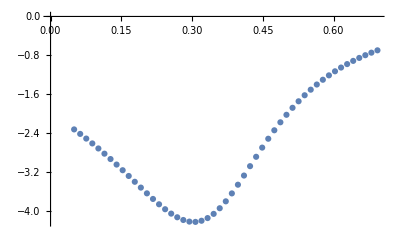

```mathematica
βlist=N@Subdivide[0.05,Log[2],50];
elist=Table[D[(β f), β,β]/.β->βlist[[i]],{i,1,Length[βlist]}];
ListPlot[Table[{βlist[[i]],elist[[i]]},{i,1,Length[βlist]}]]
```

```mathematica
D[(β f), β]/.J[k_]:>2^(k σ)J/.J->1/.σ->0.4/.β->1.2 Log[2]/2
```

-2.44007

```mathematica
Simplify[Sum[2^-j,{j,1,k}]]
```

1-2^-k

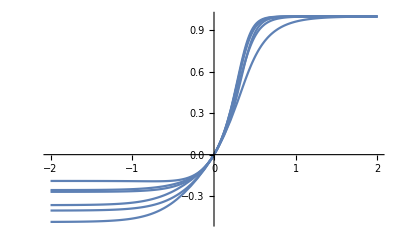

```mathematica
Plot[Table[1/2^(n-k)(D[Log[Z[n]], J[k]]/.J[k_]:>J/.β->1),{k,0,n}],{J,-2,2},GridLines->{{Log[√2]},{}}]
```

```mathematica
Y[k_]:=(Sinh[β J[k]]+Y[k-1]^2 Cosh[β J[k]])/(Cosh[β J[k]]+Y[k-1]^2 Sinh[β J[k]]);
Y[0]=Tanh[β J[0]];
```

```mathematica
f0=-1/β Log[Z[0]];
a[k_]:=β^-1 2^-k Log[Cosh[β J[k]]+Y[k-1]^2 Sinh[β J[k]]];
fn=f0-Sum[a[j],{j,1,n}];
```

```mathematica
Ysol=FullSimplify[Solve[Y==(Sinh[β J]+Cosh[β J] Y^2)/(Cosh[β J]+Sinh[β J] Y^2),Y]]/.β->1;
Jc=Log[√2];
Ytrue[J_]:=Piecewise[{{1,J≥Jc},{Y/.Ysol[[2,1]],J≤Jc}}]
```

```mathematica
Jstart=0;Jend=Jc//N;imax=20;
Jstart2=Jc//N;Jend2=1.0;
Jlist1=Table[Jstart+(Jend-Jstart)((i-1)/(imax-1)),{i,1,imax}];
Jlist2=Table[Jstart2+(Jend2-Jstart2)((i-1)/(imax-1)),{i,1,imax}];
```

```mathematica
intlist=Table[NIntegrate[Ytrue[J],{J,0,Jlist1[[i]]}],{i,1,imax}]
```

{0.,0.000168432,0.000682416,0.00155598,0.00280466,0.00444579,0.00649885,0.00898589,0.0119321,0.0153667,0.0193238,0.023844,0.0289766,0.0347827,0.0413404,0.0487536,0.0571693,0.0668136,0.078097,0.092251}

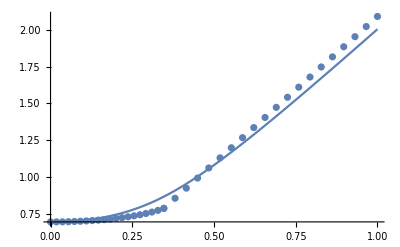

```mathematica
Show[{Plot[(-fn/.J[i_]:>J/.β->1),{J,0,Jend2}],ListPlot[Table[{Jlist1[[i]],Log[2]+intlist[[i]]},{i,1,imax}]],ListPlot[Table[{Jlist2[[i]],intlist[[-1]]+2Jlist2[[i]]},{i,1,imax}]]},PlotRange->All]
```

```mathematica
intYtrue[J_]:=Piecewise[{{J,J≥Jc},{-NIntegrate[Ytrue[JJ],{JJ,J,Jc}],J≤Jc}}]
```

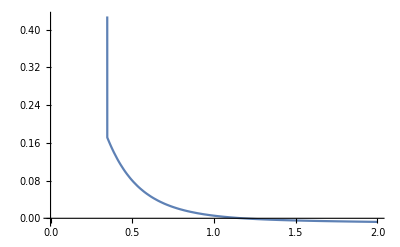

```mathematica
Plot[{(-fn/.J[i_]:>J/.β->1)-2intYtrue[J]},{J,0,2}]
```

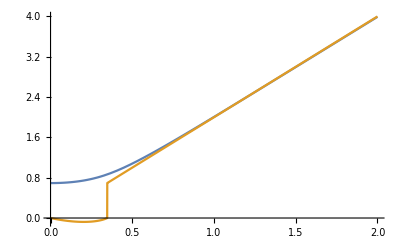

```mathematica
Plot[{-fn/.J[i_]:>J/.β->1,2intYtrue[J]},{J,0,2}]
```

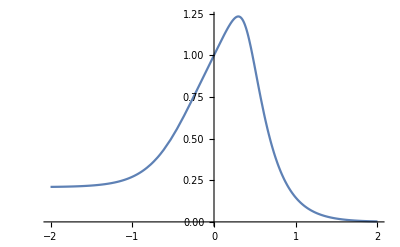

```mathematica
Plot[-(D[fn, J[0],J[0]])/.J[i_]:>J/.β->1,{J,-2,2},GridLines->{{Log[√2]},{}}]
```

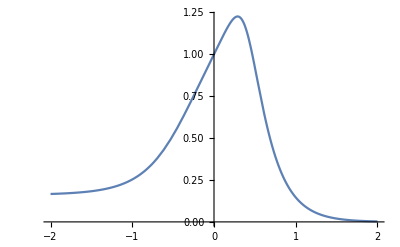

```mathematica
Plot[-(D[fn, J[0],J[0]])/.J[i_]:>J/.β->1,{J,-2,2},GridLines->{{Log[√2]},{}}]
```

```mathematica
fstar=f0-1/β Log[Cosh[β J]+Y[n]^2 Sinh[β J]];
```

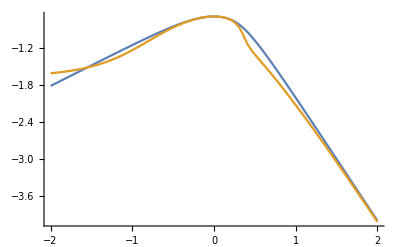

```mathematica
Plot[{fn/.J[i_]:>J/.β->1,fstar/.J[i_]:>J/.β->1},{J,-2,2}]
```

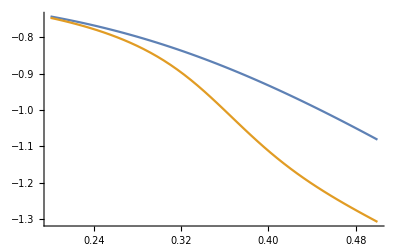

```mathematica
Plot[{fn/.J[i_]:>J/.β->1,fstar/.J[i_]:>J/.β->1},{J,0.2,0.5}]
```

```mathematica
Assuming[β>0&&J>0,FullSimplify[(Cosh[β J]+Y[0]^2 Sinh[β J])/.J[k_]:>J]]
```

Cosh[J β]+Sinh[J β] Tanh[J β]^2

```mathematica
Y[1]
```

(Sinh[β J[1]]+Cosh[β J[1]] Tanh[β J[0]]^2)/(Cosh[β J[1]]+Sinh[β J[1]] Tanh[β J[0]]^2)

```mathematica
Assuming[β>0&&J>0,FullSimplify[(Cosh[β J]+Y[2]^2 Sinh[β J])/.J[k_]:>J]]
```

Cosh[J β]+(Sinh[J β] (3+5 Cosh[4 J β]+2 Sinh[2 J β]-3 Sinh[4 J β])^2 Tanh[J β]^2)/(3+5 Cosh[4 J β]-2 Sinh[2 J β]-3 Sinh[4 J β])^2

```mathematica
Assuming[β>0&&J>0,FullSimplify[(Cosh[β J]+Y[3]^2 Sinh[β J])/.J[k_]:>J]]
```

Cosh[J β]+(16 Cosh[J β]^2 Sinh[J β]^3 (11+28 Cosh[4 J β]+25 Cosh[8 J β]-18 Sinh[4 J β]-23 Sinh[8 J β])^2)/(82 Cosh[2 J β]+117 Cosh[6 J β]+57 Cosh[10 J β]-38 Sinh[2 J β]-109 Sinh[6 J β]-55 Sinh[10 J β])^2

```mathematica
Series[(fn/.J[i_]:>J),{β,0,5}]
```

-Log[2]/β-(131071 J^2 β)/131072-(65535 J^3 β^2)/65536-(655337 J^4 β^3)/786432-(8191 J^5 β^4)/16384+(1704733 J^6 β^5)/5898240+O[β]^6

```mathematica
Series[(fn/.J[i_]:>J),{β,0,5}]
```

-Log[2]/β-(2047 J^2 β)/2048-(1023 J^3 β^2)/1024-(10217 J^4 β^3)/12288-(127 J^5 β^4)/256+(27421 J^6 β^5)/92160+O[β]^6

```mathematica
Series[%,{J,0,12}]
```

-Log[2]-(31 J^2)/32-(15 J^3)/16-(137 J^4)/192-J^5/4+(1213 J^6)/1440+(73 J^7)/24+(255551 J^8)/40320+(8623 J^9)/1008+(541889 J^10)/226800-(19115 J^11)/756-(2546181949 J^12)/29937600+O[J]^13

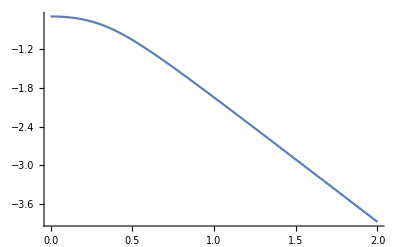

```mathematica
Plot[%,{J,0,2}]
```

```mathematica
Assuming[β>0,Simplify[Series[fn==-1/(2^n β)Log[Z[n]],{β,0,4}]]]
```

True

## Perturbation Theory

### work out the perturbation equations

```mathematica
Clear["Global`*"]
```

```mathematica
Y[k_]=Sum[Y[k,i] β^i,{i,0,6}]
```

Y[k,0]+β Y[k,1]+β^2 Y[k,2]+β^3 Y[k,3]+β^4 Y[k,4]+β^5 Y[k,5]+β^6 Y[k,6]

```mathematica
Yeqn=Series[Y[k]-(Sinh[β J[k]]+Cosh[β J[k]] Y[-1+k]^2)/(Cosh[β J[k]]+Sinh[β J[k]] Y[-1+k]^2),{β,0,6}];
```

```mathematica
Simplify[SeriesCoefficient[Series[-1/β Log[Cosh[β J[k]]+Y[k-1]^2 Sinh[β J[k]]],{β,0,4}],3]/.Y[k_,0]:>0]
```

J[k]^4/12-2 J[k] Y[-1+k,1] Y[-1+k,2]

```mathematica
Series[-β^-1 Log[2Cosh[β J0]],{β,0,4}]
```

-Log[2]/β-(J0^2 β)/2+(J0^4 β^3)/12+O[β]^5

```mathematica
SeriesCoefficient[Yeqn,{0}]
```

-Y[-1+k,0]^2+Y[k,0]

```mathematica
Simplify[SeriesCoefficient[Yeqn,{1}]]/.Y[k_,0]:>0
```

-J[k]+Y[k,1]

```mathematica
Simplify[SeriesCoefficient[Yeqn,{2}]/.Y[k_,0]:>0]
```

-Y[-1+k,1]^2+Y[k,2]

```mathematica
Simplify[SeriesCoefficient[Yeqn,{3}]/.Y[k_,0]:>0]
```

J[k]^3/3-2 Y[-1+k,1] Y[-1+k,2]+Y[k,3]

```mathematica
Simplify[SeriesCoefficient[Yeqn,{4}]/.Y[k_,0]:>0/.k->2/.Y[0,1]->J[0]/.Y[0,2]->0/.Y[0,3]->-J[0]^3/3/.Y[1,4]->1/3 (-2 J[0]^4-3 J[0]^2 J[1]^2)/.Y[1,3]->-J[1]^3/3/.Y[1,1]->J[1]/.Y[1,2]->J[0]^2]
```

-J[0]^4+(2 J[1]^4)/3+J[1]^2 J[2]^2+Y[2,4]

```mathematica
Solve[%==0,Y[1,4]]
```

{{Y[1,4]→1/3 (-2 J[0]^4-3 J[0]^2 J[1]^2)}}

```mathematica
Y[k,i]
```

```mathematica
Y[k=0,i=1]->J[0]
Y[k=0,i=2]->0
```

```mathematica
Simplify[(J[k]^3/3-2 Y[-1+k,1] Y[-1+k,2]+Y[k,3])/.k->2/.Y[0,1]->J[0]/.Y[0,2]->0/.Y[1,3]->-J[1]^3/3]
```

J[2]^3/3-2 Y[1,1] Y[1,2]+Y[2,3]

```mathematica
Yrule[0]=0;
For[i=1,i≤4,i++,
Yrule[i]=Simplify[Solve[SeriesCoefficient[Yeqn/.Table[Y[k_,j]->Yrule[j],{j,0,i-1}],i]==0,Y[k,i]][[1,1]][[2]]];
];
```

```mathematica
Simplify[Yrule[0]]
Simplify[Yrule[1]]
Simplify[Yrule[2]]
Simplify[Yrule[3]]
Simplify[Yrule[4]]
```

0

J[k]

J[-1+k]^2

2 J[-2+k]^2 J[-1+k]-J[k]^3/3

J[-2+k]^4+4 J[-3+k]^2 J[-2+k] J[-1+k]-2/3 J[-1+k]^4-J[-1+k]^2 J[k]^2

```mathematica
Simplify[Series[Yeqn,{β,0,4}]/.Table[Y[k_,j]->Yrule[j],{j,0,4}]]
```

O[β]^5

```mathematica
Simplify[Series[-1/β Log[Cosh[β J[k]]+Y[k-1]^2 Sinh[β J[k]]],{β,0,3}]/.Y[k_,0]:>0/.Y[k_,1]:>J[k]/.Y[k_,2]:>J[k-1]^2/.Y[k_,3]:>-(-2 J[-2+k]^2 J[-1+k]+J[k]^3/3)]
```

-1/2 J[k]^2 β-J[-1+k]^2 J[k] β^2+(-2 J[-2+k]^2 J[-1+k] J[k]+J[k]^4/12) β^3+O[β]^4

```mathematica
Series[-1/β Log[2Cosh[β J0]],{β,0,3}]
```

-Log[2]/β-(J0^2 β)/2+(J0^4 β^3)/12+O[β]^4

```mathematica
Frule[k_]=Simplify[∑_(j=0)^k -2^(-1+k-j) β J[j]^2]
```

∑_(j=0)^k -2^(-1-j+k) β J[j]^2

```mathematica
Simplify[{F[k]==2F[k-1]-(β J[k]^2)/2,F[0]==-(β J[0]^2)/2}/.F[k_]:>Frule[k]]
```

{β J[k]^2+2 ∑_(j=0)^k -2^(-1-j+k) β J[j]^2==4 ∑_(j=0)^(-1+k) -2^(-2-j+k) β J[j]^2,True}

```mathematica
RSolve[{F[k]==2F[k-1]-(β J[k]^2)/2,F[0]==-(β J[0]^2)/2},F[k],k]
```

{{F[k]→2^(-1+k) ∑_(K[1]=-1)^(-1+k) -2^(-1-K[1]) β J[1+K[1]]^2}}

```mathematica
RSolve[{F[k]==2F[k-1]-β^2 J[k-1]^2 J[k],F[1]==0*2F[0]-β^2 J[0]^2 J[1]},F[k],k]/.J[-1]->0
```

{{F[k]→2^(-1+k) ∑_(K[1]=-1)^(-1+k) -2^(-K[1]) β^2 J[K[1]]^2 J[1+K[1]]}}

```mathematica
Frule[k_]=Simplify[∑_(j=0)^k -2^(k-j) β^2 J[j-1]^2 J[j]]
```

∑_(j=0)^k -2^(-j+k) β^2 J[-1+j]^2 J[j]

```mathematica
Frule[0]
```

-β^2 J[-1]^2 J[0]

```mathematica
Simplify[{F[k]==2F[k-1]-β^2 J[k-1]^2 J[k],F[0]==-(β J[0]^2)/2}/.F[k_]:>Frule[k]/.k->4]
```

{True,2 β^2 J[-1]^2 J[0]==β J[0]^2}

```mathematica
Series[Tanh[β J[0]],{β,0,3}]
```

J[0] β-1/3 J[0]^3 β^3+O[β]^4

### check the answer

```mathematica
Clear[n,J,Z]
n=10;
Z[0]=2Cosh[β J[0]];
Do[Z[k]=Z[k-1]Z[k-1](Cosh[β J[k]]+1/β^2(D[Log[Z[k-1]], J[k-1]])(D[Log[Z[k-1]], J[k-1]])Sinh[β J[k]]),{k,1,n}]
```

(i = -1)

```mathematica
Table[-2^k Log[2] == SeriesCoefficient[Series[-1/β Log[Z[k]],{β,0,0}],-1],{k,0,n}]
```

{True,True,True,True,True,True,True,True,True,True,True}

(i = 0)

```mathematica
Table[0 == SeriesCoefficient[Series[-1/β Log[Z[k]],{β,0,4}],0],{k,0,n}]
```

{True,True,True,True,True,True,True,True,True,True,True}

(i = 1)

```mathematica
Table[Simplify[-Sum[2^(k-1-i)J[i]^2,{i,0,k}]==SeriesCoefficient[Series[-1/β Log[Z[k]],{β,0,4}],1]],{k,0,n}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
-Simplify[SeriesCoefficient[Series[1/(β 2^n)Log[Z[n]],{β,0,4}],1]/.J[k_]:>J[0]]
```

-(2047 J[0]^2)/2048

(i = 2)

```mathematica
Table[Simplify[(-Sum[2^(k-i)J[i-1]^2 J[i],{i,0,k}]/.J[-1]->0)==SeriesCoefficient[Series[-1/β Log[Z[k]],{β,0,4}],2]],{k,0,n}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
-Simplify[SeriesCoefficient[Series[1/(β 2^n)Log[Z[n]],{β,0,4}],2]/.J[k_]:>J[0]]
```

-(1023 J[0]^3)/1024

(i = 3)

```mathematica
Table[Simplify[(Sum[2^(k-i-2)/3(J[i]^4-24 J[i-2]^2 J[i-1]J[i]),{i,0,k}]/.J[-1]->0)==SeriesCoefficient[Series[-1/β Log[Z[k]],{β,0,4}],3]],{k,0,n}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
-Simplify[SeriesCoefficient[Series[1/(β 2^n)Log[Z[n]],{β,0,4}],3]/.J[k_]:>J[0]]
```

-(10217 J[0]^4)/12288

(i = 4)

```mathematica
Table[Simplify[(Sum[2^(k-i)((J[i-1]^2 J[i]^3)/3-J[i-2]^4 J[i]+2/3 J[i-1]^4 J[i]-4 J[i-3]^2 J[i-2]J[i-1]J[i]),{i,0,k}]/.J[-1]->0/.J[-2]->0)==SeriesCoefficient[Series[-1/β Log[Z[k]],{β,0,4}],4]],{k,0,n}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
-Simplify[SeriesCoefficient[Series[1/(β 2^n)Log[Z[n]],{β,0,4}],4]/.J[k_]:>J[0]]
```

-127/256 J[0]^5

### large-n limit

```mathematica
Clear["Global`*"]
```

```mathematica
(-J0^2)Sum[2^(-j-1)r^(2j),{j,0,Infinity}]
```

J0^2/(-2+r^2)

```mathematica
(-J0^3)Sum[2^-j r^(3j-1),{j,1,Infinity}]
```

(J0^3 r^2)/(-2+r^3)

```mathematica
(J0^4/12)Sum[2^-j(r^(4j)-24 r^(4j-5)),{j,2,Infinity}]
```

(J0^4 (24 r^3-r^8))/(24 (-2+r^4))

```mathematica
Simplify[(J0^5)(0+(1/3 r^3+2/3 r)+(1/3 r^(2+3*2)-r^2+2/3 r^(4+2)-4 r^(2 0+1+2+3))+Sum[2^-j(1/3 r^(2(j-1))r^(3j)-r^(4(j-2))r^j+2/3 r^(4(j-1))r^j-4 r^(2(j-3))r^(j-2)r^(j-1)r^j),{j,3,Infinity}])]
```

(J0^5 r (-16+24 r-8 r^2+100 r^5-9 r^6-4 r^7-42 r^10+3 r^12))/(12 (-2+r^5))

## Width and Height Symmetric Model

### parity recursions

```mathematica
Clear["Global`*"]
```

I can’t solve the Y_k recursion relation for general couplings J_k:

```mathematica
RSolve[Simplify[{Y[k]==β^-1 D[Log[Cosh[β J[k]]+Y[k-1]^2 Sinh[β J[k]]], J[k]],Y[0]==Tanh[β J[0]]}],Y[k],k]
```

RSolve[{Y[k]==(Sinh[β J[k]]+Cosh[β J[k]] Y[-1+k]^2)/(Cosh[β J[k]]+Sinh[β J[k]] Y[-1+k]^2),Tanh[β J[0]]==Y[0]},Y[k],k]

Even setting them all to be equal doesn’t change this:

```mathematica
RSolve[Simplify[{Y[k]==β^-1 D[Log[Cosh[β J[0]]+Y[k-1]^2 Sinh[β J[0]]], J[0]],Y[0]==Tanh[β J[0]]}],Y[k],k]
```

RSolve[{Y[k]==(Sinh[β J[0]]+Cosh[β J[0]] Y[-1+k]^2)/(Cosh[β J[0]]+Sinh[β J[0]] Y[-1+k]^2),Tanh[β J[0]]==Y[0]},Y[k],k]

If we are interested in the asymptotic value, then here we are in luck. This results in a cubic equation which we can solve:

```mathematica
Ysol=FullSimplify[Solve[Y==(Sinh[β J[0]]+Cosh[β J[0]] Y^2)/(Cosh[β J[0]]+Sinh[β J[0]] Y^2),Y]]
```

{{Y→1},{Y→1/2 (-1+Coth[β J[0]]-√(ⅇ^(β J[0])) Csch[β J[0]] √((-3+Coth[β J[0]]) Sinh[β J[0]]))},{Y→1/2 (-1+Coth[β J[0]]+√(ⅇ^(β J[0])) Csch[β J[0]] √((-3+Coth[β J[0]]) Sinh[β J[0]]))}}

```mathematica
FullSimplify[Ysol]
```

{{Y→1},{Y→1/2 (-1+Coth[β J[0]]-√(ⅇ^(β J[0])) Csch[β J[0]] √((-3+Coth[β J[0]]) Sinh[β J[0]]))},{Y→1/2 (-1+Coth[β J[0]]+√(ⅇ^(β J[0])) Csch[β J[0]] √((-3+Coth[β J[0]]) Sinh[β J[0]]))}}

```mathematica
Assuming[β J[0]>0,FullSimplify[Ysol]]
```

{{Y→1},{Y→1/2 (-1+Coth[β J[0]]-√(2-ⅇ^(2 β J[0])) Csch[β J[0]])},{Y→1/2 (-1+Coth[β J[0]]+√(2-ⅇ^(2 β J[0])) Csch[β J[0]])}}

```mathematica
Assuming[β J[0]<0,FullSimplify[Ysol]]
```

{{Y→1},{Y→1/2 (-1+Coth[β J[0]]-√(2-ⅇ^(2 β J[0])) Csch[β J[0]])},{Y→1/2 (-1+Coth[β J[0]]+√(2-ⅇ^(2 β J[0])) Csch[β J[0]])}}

There is a critical temperature which is positive if J_0>0 (ferromagnetic couplings):

```mathematica
βc=Log[2]/(2J[0]);
βc J[0]//N
```

0.346574

Expanding the Y^- solution around this point yields:

```mathematica
Clear[J,β]
β=βc-x;
Assuming[x>0,FullSimplify[Series[Y/.Ysol[[2,1]],{x,0,1}]]]
```

1-2 (√2 √J[0]) √x+4 J[0] x+O[x]^(3/2)

```mathematica
Y/.Ysol[[2,1]]/.β->βc-10^-4/.J[0]->1//N
```

0.972109

```mathematica
1-2 √(2(βc-β))/.β->βc-10^-4//N
```

1.-2.82843 √x

```mathematica
Clear[J,β]
```

Plug in some values:

```mathematica
FullSimplify[Ysol/.β->1.01βc/.J[0]->1]//N
FullSimplify[Ysol/.β->0.99βc/.J[0]->1]//N
```

{{Y→1.},{Y→0.98628-0.165082 ⅈ},{Y→0.98628+0.165082 ⅈ}}

{{Y→1.},{Y→0.84604},{Y→1.18198}}

Calculate the exact Y_k:

```mathematica
Clear[k,Y,n,J,Ytrue,Yks,line1,plot,ticks,newticks]
n=10;
Y[0]=Tanh[β J[0]];
For[k=1,k≤n,k++,
Y[k]=(Sinh[β J[0]]+Cosh[β J[0]] Y[-1+k]^2)/(Cosh[β J[0]]+Sinh[β J[0]] Y[-1+k]^2);
];
Clear[k]
```

```mathematica
Clear[J,Ytrue,Yks,line1,plot,ticks,newticks]
J[0]=1;
line1=Line[{{βc,0},{βc,1.1}}];
Ytrue[β_]:=Piecewise[{{1,β≥βc},{Y/.Ysol[[2,1]],β≤βc}}];
Yks=Table[Y[k],{k,0,n}];
plot1=Plot[Yks,{β,0,2},PlotRange->All,LabelStyle->Black,PlotLabels->Table["n = "<>ToString[k],{k,0,n}],PlotStyle->Directive[Thickness[0.003],Black]];
ticks=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[plot1][[1]];
newticks={{βc/.J[0]->1,"β_c"}}~Join~ticks;
plot1=Show[{plot1,Plot[Ytrue[β],{β,0,2},PlotPoints->20000,PlotStyle->Directive[{Dashed,Black}]]},Ticks->{newticks,Automatic},ImageSize->400,Epilog->{Directive[{Thin,Red,Dashed}],line1,Text[Style["parity locked phase",16],Scaled[{0.55,0.5}]]}];
plot1=Labeled[plot1,{"P_n","β"},{Left,Bottom},LabelStyle->Directive[Black]]
```

-Graphics-P_nβ

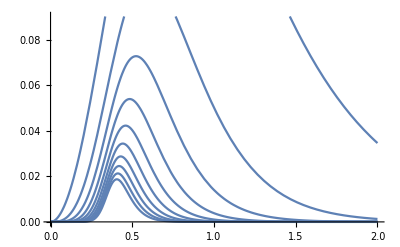

```mathematica
Plot[Table[Y[k]-Y[k-1],{k,1,n}],{β,0,2}]
```

```mathematica
Clear[J,Ytrue,Yks,line1,plot,ticks,newticks]
J[0]=-1;
Ytrue[β_]=Y/.Ysol[[2,1]];
Yks=Table[Y[k],{k,0,n}];
plot2=Plot[Yks,{β,0,2},PlotRange->All,PlotLabels->Table["n = "<>ToString[k],{k,0,n}],PlotStyle->Directive[Thickness[0.003],Black]];
ticks=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[plot2][[1]];
newticks={{βc/.J[0]->1,"β_c"}}~Join~ticks;
plot2=Show[{plot2,Plot[Ytrue[β],{β,0,2},PlotPoints->20000,PlotStyle->Directive[{Dashed,Black}]]},Ticks->{newticks,Automatic},ImageSize->400];
plot2=Labeled[plot2,{"P_n","β"},{Left,Bottom},LabelStyle->Directive[Black]]
```

-Graphics-P_nβ

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/gavin/Dropbox/Research/Machine Learning/Google Collaboration/hierarchical

```mathematica
Export["Pkplot_Jpositive.pdf",plot1];
Export["Pkplot_Jnegative.pdf",plot2];
```

```mathematica
Clear[J]
J[0]=1;
```

```mathematica
Y0=Y/.Ysol[[1,1]];
Yminus=Y/.Ysol[[2,1]];
Yplus=Y/.Ysol[[3,1]];
```

```mathematica
Plot[{Yminus,Y0,Yplus},{β,0,βc},PlotLabels->{"(P_∞)^(-)","(P_∞)^(0)","(P_∞)^(+)"}]
```

-Graphics-

```mathematica
Clear[J]
J[0]=-1;
```

```mathematica
Y0=Y/.Ysol[[1,1]];
Yminus=Y/.Ysol[[2,1]];
Yplus=Y/.Ysol[[3,1]];
```

```mathematica
βc
```

-Log[2]/2

```mathematica
Yminus
```

1/2 (-1-Coth[β]+√(ⅇ^-β) Csch[β] √(-(-3-Coth[β]) Sinh[β]))

```mathematica
Plot[{Yminus,Y0,Yplus},{β,0,10Abs[βc]},PlotLabels->{"(P_∞)^(-)","(P_∞)^(0)","(P_∞)^(+)"}]
```

-Graphics-

## Tutte Polynomial

```mathematica
Clear["Global`*"]
```

```mathematica
TuttePolynomial[CycleGraph[5],{x,y}]
```

x+x^2+x^3+x^4+y

loop

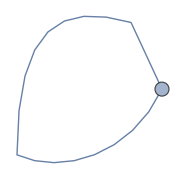

y

```mathematica
G=Graph[{1<->1}]
TuttePolynomial[G,{x,y}]
```

```mathematica
Subsets[{"a"}]
```

{{},{a}}

bridge or isthmus

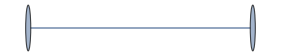

x

-Graphics-

```mathematica
G=Graph[{1<->2}]
TuttePolynomial[G,{x,y}]
```

## Spin-Glass HREM calculation

```mathematica
Clear["Global`*"]
βlist=N@Subdivide[0.05,10,100];
gclist=Table[{βlist[[i]],√(2NIntegrate[Exp[-1/2 x^2]/(√(2π))Tanh[βlist[[i]] x]^2,{x,-Infinity,Infinity}])},{i,1,Length[βlist]}];
```

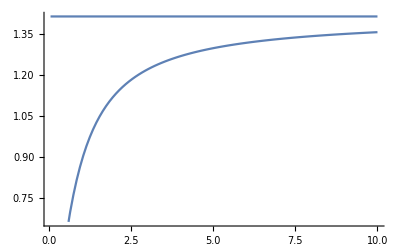

```mathematica
Show[{Plot[√2,{β,Min[βlist],Max[βlist]}],ListLinePlot[gclist]},PlotRange->All]
```

```mathematica
Simplify[Series[Tanh[β x]^2,{β,βc,1}]]
```

Tanh[x βc]^2+2 x Sech[x βc]^2 Tanh[x βc] (β-βc)+O[β-βc]^2

```mathematica
Series[1/(1-1/(1+y (β-βc))),{β,βc,1}]
```

1/(y (β-βc))+1+O[β-βc]^2

## Numerical Investigation of Partition Function

### General Model

```mathematica
Clear["Global`*"]
```

Pick a value of n:

```mathematica
n=5;
Nn=2^n;
Print["number of spins N = ", 2^n];
Print["number of states 2^N = ",2^Nn//N];
```

number of spins N = 32

number of states 2^N = 4.29497×10^9

Compute the partition function for general couplings and temperature using the recursion:

```mathematica
Clear[Z,Y]
Do[Z[0,p]=2Cosh[β J[0,p]],{p,1,2^n}];
Do[Y[0,p]=Tanh[β J[0,p]],{p,1,2^n}];
For[k=1,k≤n,k++,
For[p=1,p≤2^n,p++,
Z[k,p]=Z[k-1,2p-1]Z[k-1,2p](Cosh[β J[k,p]]+Sinh[β J[k,p]]Y[k-1,2p-1]Y[k-1,2p]);
Y[k,p]=β^-1 D[Log[Z[k,p]], J[k,p]];
];];
```

Pick a random draw of the interactions, letting the standard deviation be a function of tree height:

```mathematica
Tlist=N@Subdivide[0.1,5,20];
βlist=1/Tlist;
flist=Table[0,{i,1,Length[βlist]}];
g=0.3;
numDisorder=6;

For[i=1,i≤Length[βlist],i++,
β=βlist[[i]];
σ[kk_]=g^k;
f=0;
For[j=1,j≤numDisorder,j++,
Couplings=Table[RandomVariate[NormalDistribution[1,σ[k]]],{k,0,n},{p,1,2^(n-k)}];
CouplingRules=Flatten[Table[J[k,p]->1+0Couplings[[k+1,p]],{k,0,n},{p,1,2^(n-k)}]];
f+=-β^-1/(Nn numDisorder)Log[Z[n,1]/.CouplingRules];
];
flist[[i]]=f
];
```

```mathematica
(**)
```

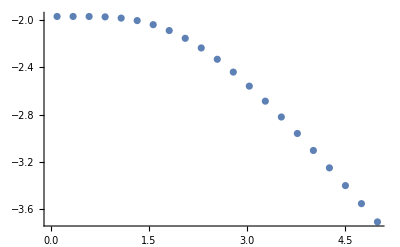

```mathematica
ListPlot[Table[{Tlist[[i]],flist[[i]]},{i,1,Length[βlist]}],PlotRange->All]
```

```mathematica
βc=Log[2]/2;
Tc=1/βc//N
```

2.88539

```mathematica
fInterp=Interpolation[Table[{Tlist[[i]],flist[[i]]},{i,1,Length[βlist]}]];
```

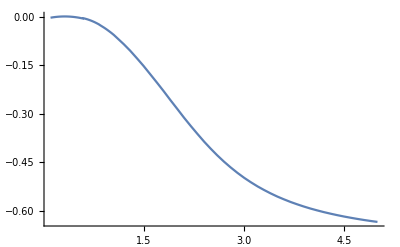

```mathematica
Plot[fInterp'[T],{T,0.1,5}]
```

```mathematica
√2 NIntegrate[Exp[-1/2 x^2]/(√(2π))Tanh[β x]^2,{x,-Infinity,Infinity}]
```

0.362663

### Height and Width Symmetric Model

```mathematica
Clear["Global`*"]
```

Pick a value of n:

```mathematica
n=4;
Nn=2^n;
Print["number of spins N = ", 2^n];
Print["number of states 2^N = ",2^Nn//N];
```

number of spins N = 16

number of states 2^N = 65536.

Compute the partition function for general couplings and temperature using the recursion:

```mathematica
Z[0]=2Cosh[β J[0]];
For[k=1,k≤n,k++,
Z[k]=Z[k-1]^2(Cosh[β J[k]]+1/β^2(D[Log[Z[k-1]], J[k-1]])^2 Sinh[β J[k]]);
];
```

```mathematica
FullSimplify[Log[Z[n]/.J[k_]:>1]]
```

Log[1280 ⅇ^(-11 β)+1856 ⅇ^(-9 β)+6352 ⅇ^(-7 β)+6304 ⅇ^(-5 β)+10032 ⅇ^(-3 β)+9457 ⅇ^-β+8144 ⅇ^β+7880 ⅇ^(3 β)+4528 ⅇ^(5 β)+4492 ⅇ^(7 β)+1776 ⅇ^(9 β)+1880 ⅇ^(11 β)+528 ⅇ^(13 β)+662 ⅇ^(15 β)+112 ⅇ^(17 β)+184 ⅇ^(19 β)+16 ⅇ^(21 β)+44 ⅇ^(23 β)+8 ⅇ^(27 β)+ⅇ^(31 β)]

```mathematica
Clear[n]
```

```mathematica
RSolve[a[n+1]==Exp[β J](a[n]^2+(1-a[n])^2),a[n],n]
```

RSolve[a[1+n]==ⅇ^(J β) ((1-a[n])^2+a[n]^2),a[n],n]

```mathematica
α=(y+1)/2;
```

```mathematica
recursion1=2(Exp[β J](α^2+(1-α)^2))/(Exp[β J](α^2+(1-α)^2)+Exp[-β J](2α(1-α)))-1;
recursion2=(Sinh[β J]+y^2 Cosh[β J])/(Cosh[β J]+y^2 Sinh[β J]);
```

```mathematica
Simplify[recursion1==recursion2]
```

True

```mathematica
Simplify[Series[recursion1,{β,0,2}]]
```

y^2+(J-J y^4) β+J^2 y^2 (-1+y^4) β^2+O[β]^3

```mathematica
Simplify[Series[recursion2,{β,0,2}]]
```

y^2+(J-J y^4) β+J^2 y^2 (-1+y^4) β^2+O[β]^3

```mathematica
recursion2
```

(y^2 Cosh[J β]+Sinh[J β])/(Cosh[J β]+y^2 Sinh[J β])

```mathematica
FullSimplify[Solve[α-(Exp[β J](α^2+(1-α)^2))/(Exp[β J](α^2+(1-α)^2)+Exp[-β J](2α(1-α)))==0,α]]
```

{{α→1},{α→1/(1+ⅇ^(-2 J β) √(-ⅇ^(2 J β) (-2+ⅇ^(2 J β))))},{α→1/(1-ⅇ^(-2 J β) √(-ⅇ^(2 J β) (-2+ⅇ^(2 J β))))}}

```mathematica
.14
```

Pick a random draw of the interactions, letting the standard deviation be a function of tree height:

```mathematica
Tlist=N@Subdivide[0.1,3,20];
βlist=1/Tlist;
flist=Table[0,{i,1,Length[βlist]}];
g=0.3;

For[i=1,i≤Length[βlist],i++,
β=βlist[[i]];
σ[kk_]=g^k;
Couplings=1+0Table[RandomVariate[NormalDistribution[1,σ[k]]],{k,0,n}];
CouplingRules=Flatten[Table[J[k]->Couplings[[k+1]],{k,0,n},{p,1,2^(n-k)}]];
flist[[i]]=-1/(Nn β)Log[Z[n]/.CouplingRules];
];
```

```mathematica
(**)
```

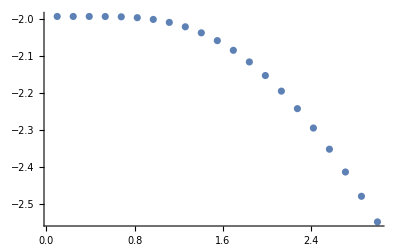

```mathematica
ListPlot[Table[{Tlist[[i]],flist[[i]]},{i,1,Length[βlist]}],PlotRange->All]
```

```mathematica
βc=Log[2]/2;
Tc=1/βc//N
```

2.88539

```mathematica
fInterp=Interpolation[Table[{Tlist[[i]],flist[[i]]},{i,1,Length[βlist]}]];
```

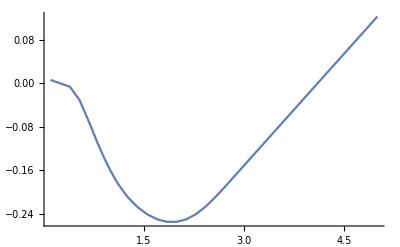

```mathematica
Plot[fInterp''[T],{T,0.1,5}]
```

```mathematica
√2 NIntegrate[Exp[-1/2 x^2]/(√(2π))Tanh[β x]^2,{x,-Infinity,Infinity}]
```

0.362663

```mathematica
s[i_]=2 b[i]-1;
```

```mathematica
Simplify[s[1]+s[2]+s[3]+s[4]+s[1]s[2]+s[3]s[4]+s[1]s[2]s[3]s[4]]
```

-4+2 b[1]+2 b[2]+(-1+2 b[1]) (-1+2 b[2])+2 b[3]+2 b[4]+(-1+2 b[3]) (-1+2 b[4])+(-1+2 b[1]) (-1+2 b[2]) (-1+2 b[3]) (-1+2 b[4])

```mathematica
Expand[%]
```

-1-2 b[1]-2 b[2]+8 b[1] b[2]-2 b[3]+4 b[1] b[3]+4 b[2] b[3]-8 b[1] b[2] b[3]-2 b[4]+4 b[1] b[4]+4 b[2] b[4]-8 b[1] b[2] b[4]+8 b[3] b[4]-8 b[1] b[3] b[4]-8 b[2] b[3] b[4]+16 b[1] b[2] b[3] b[4]

## Gaussian Disordered Model

```mathematica
Clear["Global`*"]
```

Introduce the Hamiltonian of the (k,p) sub-system:

```mathematica
H[0,p_]=-J[0,p]s[p];
H[k_,p_]:=H[k-1,2p-1]+H[k-1,2p]-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}];
```

Pick a value of n:

```mathematica
n=5;
Nn=2^n;
Print["number of spins N = ", 2^n];
Print["number of states 2^N = ", 2^Nn];
```

number of spins N = 32

number of states 2^N = 4294967296

Compute the partition function for general couplings and temperature using the recursion:

```mathematica
Clear[Z,Y]
Do[Z[0,p]=2Cosh[β J[0,p]],{p,1,2^n}];
Do[Y[0,p]=Tanh[β J[0,p]],{p,1,2^n}];
For[k=1,k≤n,k++,
For[p=1,p≤2^n,p++,
Z[k,p]=Z[k-1,2p-1]Z[k-1,2p](Cosh[β J[k,p]]+Sinh[β J[k,p]]Y[k-1,2p-1]Y[k-1,2p]);
Y[k,p]=β^-1 D[Log[Z[k,p]], J[k,p]];
];];
```

Pick a random draw of the interactions, letting the standard deviation be a function of tree height:

```mathematica
npoints=200;βstart=0.1;βend=5;
βlist=Table[βstart+(βend-βstart)(i-1)/(npoints-1),{i,1,npoints}];
paritylist=Table[0,{i,1,npoints}];
ndisorder=200;
For[i=1,i≤ndisorder,i++,
σ[kk_]=1;
Couplings=Table[RandomVariate[NormalDistribution[1,σ[k]]],{k,0,n},{p,1,2^(n-k)}];
CouplingRules=Flatten[Table[J[k,p]->Couplings[[k+1,p]],{k,0,n},{p,1,2^(n-k)}]];
HH=H[n,1]/.CouplingRules;
paritylist+=(1/(β ndisorder)D[Log[Z[n,1]], J[n,1]])/.CouplingRules/.β->βlist;
];
```

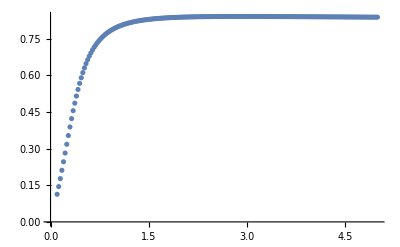

```mathematica
ListPlot[Table[{βlist[[i]],paritylist[[i]]},{i,1,npoints}],PlotRange->All]
```

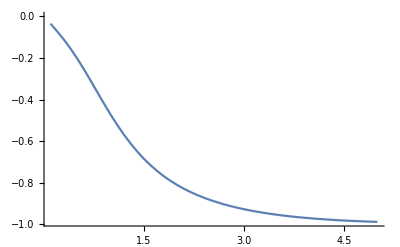

```mathematica
Plot[(1/β D[Log[Z[n,1]], J[n,1]])/.CouplingRules,{β,0.1,5}]
```

## +/- J model

```mathematica
Clear["Global`*"]
```

Plot the phase diagram

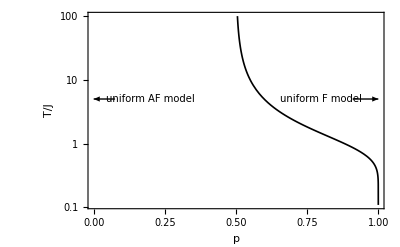

```mathematica
TNishimori[p_]=(1/2 Log[p/(1-p)])^-1;
plot=LogPlot[TNishimori[p],{p,1/2,1},PlotRange->{{0,1},{0,100}},Frame->True,FrameLabel->{"p","T/J"},GridLines->{{1/2},{}},PlotStyle->Directive[Thickness[0.003],Black],LabelStyle->Black,ImageSize->400,Epilog->({{
Inset[Style["uniform AF model",10],{0.2,5}] ,
Arrow[{{0.075,5},{0,5}}],
Inset[Style["uniform F model",10],{0.8,5}] ,
Arrow[{{0.91,5},{1,5}}]}}/.{x_,y_?NumericQ}:>{x,Log[y]})]
```

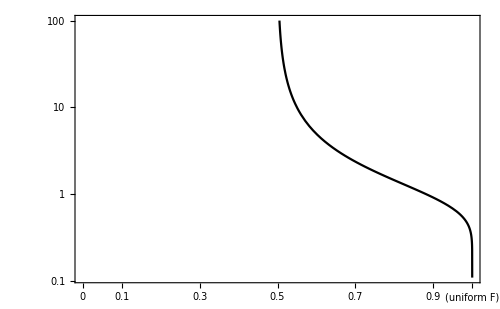
-Graphics-T/Jp

```mathematica
plot=LogPlot[TNishimori[p],{p,1/2,1},PlotRange->{{0,1},{0,100}},PlotStyle->Black,Frame->True,FrameStyle->Black,FrameTicks->{{Automatic,Automatic},{{0,{0,Style["\n(uniform AF)",Black,14]},0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,{1,Style["\n(uniform F)",Black,14]}},None}},Axes->False,GridLines->{{1/2},{}},GridLinesStyle->Directive[Black,Thickness[0.001],Dashed],Method->{"GridLinesInFront"->True},PlotRangePadding->0,ImageSize->500];
plot=Labeled[plot,{"T/J","p"},{Left,Bottom},LabelStyle->Directive[FontSize->15,Black]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Nishimori.pdf",plot];
```

```mathematica
(*Epilog->{Inset[LogPlot[TNishimori[p],{p,0.99,1},Frame->True,FrameStyle->Black,PlotStyle->Black,PlotRange->{{0.99,1},{0,10}}],{0.8,3},Automatic,Scaled[.4]],PointSize->0.02,Point[{{1,Log[Log[2]/2]}}]}*)
```

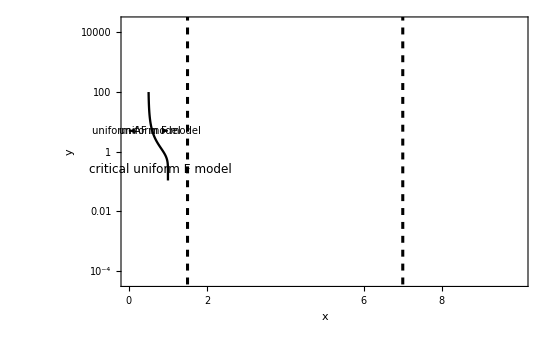

```mathematica
Show[plot,Frame->True,FrameLabel->{"x","y"},FrameTicks->{{Automatic,None},{{0,{1.5,Style["P1\n1.5",Red,14]},2,4,6,{7,Style["P2\n7.0",Red,14]},8,10},None}},Axes->False,GridLines->{{1.5,7},{}},GridLinesStyle->Directive[Black,Thickness[0.004],Dashed],Method->{"GridLinesInFront"->True},PlotRange->{{0,10},{-10,10}},PlotRangePadding->0,ImageSize->550]
```

```mathematica
Clear[J,Ytrue,Yks,line1,plot,ticks,newticks]
J[0]=1;
line1=Line[{{βc,0},{βc,1.1}}];
Ytrue[β_]:=Piecewise[{{1,β≥βc},{Y/.Ysol[[2,1]],β≤βc}}];
Yks=Table[Y[k],{k,0,n}];
plot1=Plot[Yks,{β,0,2},PlotRange->All,LabelStyle->Black,PlotLabels->Table["n = "<>ToString[k],{k,0,n}],PlotStyle->Directive[Thickness[0.003],Black]];
ticks=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[plot1][[1]];
newticks={{βc/.J[0]->1,"β_c"}}~Join~ticks;
plot1=Show[{plot1,Plot[Ytrue[β],{β,0,2},PlotPoints->20000,PlotStyle->Directive[{Dashed,Black}]]},Ticks->{newticks,Automatic},ImageSize->400,Epilog->{Directive[{Thin,Red,Dashed}],line1,Text[Style["parity locked phase",16],Scaled[{0.55,0.5}]]}];
plot1=Labeled[plot1,{"Y_(n, 1)","β"},{Left,Bottom},LabelStyle->Directive[Black]]
```

Introduce the Hamiltonian of the (k,p) sub-system:

```mathematica
H[0,p_]=-J[0,p]s[p];
H[k_,p_]:=H[k-1,2p-1]+H[k-1,2p]-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}];
```

Pick a value of n:

```mathematica
n=4;
Nn=2^n;
Print["number of spins N = ", 2^n];
Print["number of states 2^N = ", 2^Nn];
```

number of spins N = 16

number of states 2^N = 65536

Compute the partition function for general couplings and temperature using the recursion:

```mathematica
Clear[Z,Y]
Do[Z[0,p]=2Cosh[β J[0,p]],{p,1,2^n}];
Do[Y[0,p]=Tanh[β J[0,p]],{p,1,2^n}];
For[k=1,k≤n,k++,
For[p=1,p≤2^n,p++,
Z[k,p]=Z[k-1,2p-1]Z[k-1,2p](Cosh[β J[k,p]]+Sinh[β J[k,p]]Y[k-1,2p-1]Y[k-1,2p]);
Y[k,p]=β^-1 D[Log[Z[k,p]], J[k,p]];
];];
```

Check my calculation of the energy at the Nishimori temperature:
E(β_N)=-L J tanh(β_N J), where L=2N-1 is the number of bonds.

```mathematica
βN[prob_]=1/2 Log[prob/(1-prob)];
```

```mathematica
prob=0.8;
ndisorder=200;
Enlist={};
For[i=1,i≤ndisorder,i++,
Couplings=Table[2RandomVariate[BernoulliDistribution[prob]]-1,{k,0,n},{p,1,2^(n-k)}];
CouplingRules=Flatten[Table[J[k,p]->Couplings[[k+1,p]],{k,0,n},{p,1,2^(n-k)}]];
AppendTo[Enlist,(-D[Log[Z[n,1]], β])/.CouplingRules/.β->βN[prob]];
];
```

```mathematica
-(2^(n+1)-1)Tanh[βN[prob]]
```

-18.6

```mathematica
{Mean[Enlist]-2(√Variance[Enlist])/(Length[Enlist]-1),Mean[Enlist]+2(√Variance[Enlist])/(Length[Enlist]-1)}
```

{-18.6746,-18.613}

Do a scan over parameter space:

```mathematica
βc=Log[2]/2.0
```

0.346574

```mathematica
ndisorder=15;
probmin=0.0;
probmax=1;
imax=10;
problist=Table[probmin+((i-1)/(imax-1))(probmax-probmin),{i,1,imax}]
```

{0.,0.111111,0.222222,0.333333,0.444444,0.555556,0.666667,0.777778,0.888889,1.}

```mathematica
Enlist={};
Flist={};
Ylist={};
For[i=1,i≤imax,i++,
prob=problist[[i]];
En=0;F=0;YY=0;

For[j=1,j≤ndisorder,j++,
Couplings=Table[2RandomVariate[BernoulliDistribution[prob]]-1,{k,0,n},{p,1,2^(n-k)}];
CouplingRules=Flatten[Table[J[k,p]->Couplings[[k+1,p]],{k,0,n},{p,1,2^(n-k)}]];
En+=(-D[Log[Z[n,1]], β])/.CouplingRules/.β->βc;
F+=-Log[Z[n,1]]/β/.CouplingRules/.β->βc;
YY+=Y[n,1]/.CouplingRules/.β->βc;
];
AppendTo[Enlist,En/ndisorder];
AppendTo[Flist,F/ndisorder];
AppendTo[Ylist,YY/ndisorder];
];
```

```mathematica
Ylist
```

{-0.269046,-0.200701,-0.118788,-0.248793,-0.132048,0.0612638,0.139629,0.198694,0.411667,0.607478}

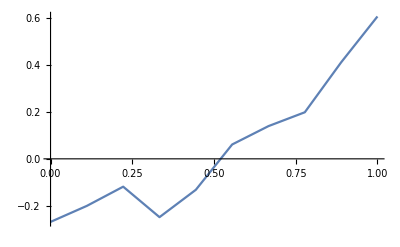

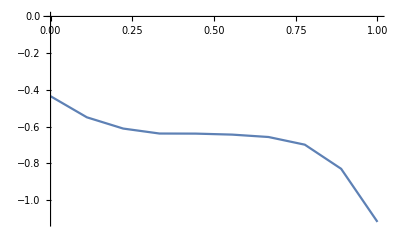

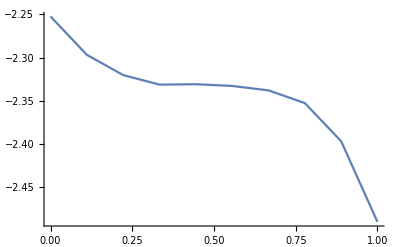

```mathematica
ListLinePlot[Table[{problist[[i]],Ylist[[i]]},{i,1,Length[Enlist]}]]
ListLinePlot[Table[{problist[[i]],Enlist[[i]]/2^n},{i,1,Length[Enlist]}]]
ListLinePlot[Table[{problist[[i]],Flist[[i]]/2^n},{i,1,Length[Enlist]}]]
```

```mathematica
Simplify[p Tanh[β J]+(1-p)Tanh[-β J]]
```

(-1+2 p) Tanh[J β]

## Equivalence b/w P and Prob recursion relations

```mathematica
Clear["Global`*"]
```

```mathematica
ProbRecursion=α[n]-(Exp[β J[n]](α[n-1]^2+(1-α[n-1])^2))/(Exp[β J[n]](α[n-1]^2+(1-α[n-1])^2)+Exp[-β J[n]](2α[n-1](1-α[n-1])));
α[n_]=1/2(Y[n]+1);
```

```mathematica
FullSimplify[Solve[ProbRecursion==0,Y[n]]]
```

{{Y[n]→(1+Coth[β J[n]] Y[-1+n]^2)/(Coth[β J[n]]+Y[-1+n]^2)}}

```mathematica
Simplify[Sinh[β J[n]](1+Coth[β J[n]] Y[-1+n]^2)]
```

Sinh[β J[n]]+Cosh[β J[n]] Y[-1+n]^2

```mathematica
Simplify[Sinh[β J[n]](Coth[β J[n]]+Y[-1+n]^2)]
```

Cosh[β J[n]]+Sinh[β J[n]] Y[-1+n]^2

## Sub-Parity recursions

```mathematica
Clear["Global`*"]
```

```mathematica
Simplify[D[((Sinh[β J]+PL PR Cosh[β J])/(Cosh[β J]+PL PR Sinh[β J])), PL]]
```

PR/(Cosh[J β]+PL PR Sinh[J β])^2

```mathematica
FullSimplify[P(1+((1-PR^2 PL^2)Sinh[β J])/(Cosh[β J]+PL PR Sinh[β J])^3 Sum[(PR/(Cosh[J β]+PL PR Sinh[J β])^2)^(L-l),{l,0,L-1}])/.PL->P/.PR->P]
```

P (1+(P (-1+P^4) Sinh[J β] (-1+(P/((Cosh[J β]+P^2 Sinh[J β])^2))^L))/((Cosh[J β]+P^2 Sinh[J β])^3 (Cosh[J β]^2+P (-1+P^3 Sinh[J β]^2+P Sinh[2 J β]))))

```mathematica
%/.P->1-const x
```

(1-const x) (1+((1-const x) (-1+(1-const x)^4) Sinh[J β] (-1+((1-const x)/((Cosh[J β]+(1-const x)^2 Sinh[J β])^2))^L))/((Cosh[J β]+(1-const x)^2 Sinh[J β])^3 (Cosh[J β]^2+(1-const x) (-1+(1-const x)^3 Sinh[J β]^2+(1-const x) Sinh[2 J β]))))

```mathematica
FullSimplify[Series[%,{x,0,1}]]
```

1+const (-1-2 ⅇ^(-4 J β) (-1+(ⅇ^(-2 J β))^L)) x+O[x]^2

```mathematica
FullSimplify[%/.β->Log[2]/(2 J)]
```

1-2^(-1-L) (1+2^L) const x+O[x]^2

## Masoud - “Backbone” Analysis

### General Case

```mathematica
Clear["Global`*"]
```

Introduce the Hamiltonian of the (k,p) sub-system:

```mathematica
H[0,p_]=-J[0,p]s[p];
H[k_,p_]:=H[k-1,2p-1]+H[k-1,2p]-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}];
```

Pick a value of n:

```mathematica
n=4;
Nn=2^n;
Print["number of spins N = ", 2^n];
Print["number of states 2^N = ", 2^Nn];
```

number of spins N = 16

number of states 2^N = 65536

Compute the partition function for general couplings and temperature using the recursion:

```mathematica
Clear[Z,Y]
Do[Z[0,p]=2Cosh[β J[0,p]],{p,1,2^n}];
Do[Y[0,p]=Tanh[β J[0,p]],{p,1,2^n}];
For[k=1,k≤n,k++,
For[p=1,p≤2^n,p++,
Z[k,p]=Z[k-1,2p-1]Z[k-1,2p](Cosh[β J[k,p]]+Sinh[β J[k,p]]Y[k-1,2p-1]Y[k-1,2p]);
Y[k,p]=β^-1 D[Log[Z[k,p]], J[k,p]];
];];
```

Pick a random draw of the interactions, letting the standard deviation be a function of tree height:

```mathematica
σ[kk_]=1;
Couplings=Table[RandomVariate[NormalDistribution[1,0.001σ[k]]],{k,0,n},{p,1,2^(n-k)}];

Couplings=Table[2RandomVariate[BernoulliDistribution[0.5]]-1,{k,0,n},{p,1,2^(n-k)}];

CouplingRules=Flatten[Table[J[k,p]->Couplings[[k+1,p]],{k,0,n},{p,1,2^(n-k)}]];
HH=H[n,1]/.CouplingRules;
```

```mathematica
Show[{Plot[σ[k],{k,0,n}],ListPlot[Table[{k,Sqrt[Variance[Couplings[[k+1]]]]},{k,0,n-1}]]},PlotRange->All]
```

-Graphics-

Compute the ground state of a sub-system by brute force:

```mathematica
GroundStateBrute[k_,p_]:=
Module[{gs,spinlist,states,Enlist},
spinlist=Table[s[i],{i,1+(p-1)2^k,p 2^k}];
states=Flatten[Outer[List,##]&@@Table[{-1,1},{2^k}],2^k-1];
Enlist = {};
For[i=1,i≤2^(2^k),i++,
AppendTo[Enlist,H[k,p]/.CouplingRules/.Table[spinlist[[j]]->states[[i,j]],{j,1,2^k}]];
];
gs=states[[Position[Enlist,Min[Enlist]][[1,1]]]];
gs]
```

Compute the ground state of a sub-system using the recursive property. This is the most efficient version of the algorithm, where I only consider O(1) new states at each iteration.

```mathematica
listProduct[x_List]:=Times@@x
```

```mathematica
GroundStateNew[k_,p_]:=
Module[{spinlist,state0,state1,statesA,statesB,state00,state01,state10,En00,En01,En10,stateList,EnList,sortedpairs},
spinlist=Table[s[i],{i,1+(p-1)2^k,p 2^k}];
If[k==0,
state0={Sign[J[k,p]/.CouplingRules]};
state1={-Sign[J[k,p]/.CouplingRules]};
];
If[k>0,
(* get the 00, 01, and 10 states *)
statesA=GroundStateNew[k-1,2p-1];
statesB=GroundStateNew[k-1,2p];
state00=Join[statesA[[1]],statesB[[1]]];
state01=Join[statesA[[1]],statesB[[2]]];
state10=Join[statesA[[2]],statesB[[1]]];
En00=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state00[[j]],{j,1,2^k}];
En01=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state01[[j]],{j,1,2^k}];
En10=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state10[[j]],{j,1,2^k}];
(* compile a sorted list of states and energies *)
stateList={state00,state01,state10};
EnList={En00,En01,En10};
sortedpairs = SortBy[Transpose[{EnList,stateList}],First];
EnList=Table[sortedpairs[[i,1]],{i,1,3}];
stateList=Table[sortedpairs[[i,2]],{i,1,3}];
state0=stateList[[1]];
If[listProduct[stateList[[2]]]==-listProduct[state0],state1=stateList[[2]];,state1=stateList[[3]];];
];
(* return the lowest and second-lowest energy state *)
{state0,state1}]
```

Compute the ground state of a sub-system using the recursive property. This is a less efficient version of the algorithm. At step k I consider all 2^k states which are 1 spin-flip away from my current state.

```mathematica
GroundState[k_,p_]:=
Module[{state0,state,En,EnTemp,stateTemp,spinlist},
spinlist=Table[s[i],{i,1+(p-1)2^k,p 2^k}];
If[k==0,state={Sign[J[k,p]/.CouplingRules]};];
If[k>0,
state0=Join[GroundState[k-1,2p-1],GroundState[k-1,2p]];
state=state0;
En=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->state[[j]],{j,1,2^k}];
For[i=1,i≤2^k,i++,
stateTemp=state0;
stateTemp[[i]]=-stateTemp[[i]];
EnTemp=H[k,p]/.CouplingRules/.Table[spinlist[[j]]->stateTemp[[j]],{j,1,2^k}];
If[EnTemp<En,state=stateTemp;En=EnTemp];
];
];
state]
```

Check that these all agree:

```mathematica
Table[GroundState[k,p]==GroundStateNew[k,p][[1]],{k,0,n},{p,1,2^(n-k)}]
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,False,False,False,False,True},{True,True,True,False},{True,False},{False}}

```mathematica
Table[GroundState[k,p]==GroundStateBrute[k,p],{k,0,n},{p,1,2^(n-k)}]
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,False,False,False,False,True},{True,True,True,False},{True,False},{False}}

introduce a function that tests whether a configuration is a local minima:

```mathematica
LocalMinQ[spins_]:=
Module[{localMin=True},
E1=HH/.Table[s[j]->spins[[j]],{j,1,2^n}];
p=1;
While[p≤2^n&&localMin==True,
spinstmp=spins;
spinstmp[[p]]=-spinstmp[[p]];
E2=HH/.Table[s[j]->spinstmp[[j]],{j,1,2^n}];
If[E2<E1,localMin=False;];
p+=1;
];
localMin]
```

compute the partition function, spectrum, and number of local minima by brute-force:

```mathematica
states=Flatten[Outer[List,##]&@@Table[{-1,1},{Nn}],Nn-1];
```

```mathematica
partitionFunc=0;
Enlist = {};
Enlist0={};
Maglist={};
LocalMinima={};
For[i=1,i≤2^Nn,i++,
AppendTo[Enlist0,H[n]/.Table[s[j]->states[[i,j]],{j,1,2^n}]];
AppendTo[Enlist,HH/.Table[s[j]->states[[i,j]],{j,1,2^n}]];
AppendTo[Maglist,Total[states[[i]]]];
If[LocalMinQ[states[[i]]],AppendTo[LocalMinima,states[[i]]]];
partitionFunc+=Exp[-HH]/.Table[s[j]->states[[i,j]],{j,1,2^n}];
];
Clear[i]
```

```mathematica
Histogram[(Maglist/2^n//N),40,"ProbabilityDensity"]
```

-Graphics-

```mathematica
Histogram[Enlist,40,"ProbabilityDensity"]
```

-Graphics-

sort the states by energy:

```mathematica
sortedpairs = SortBy[Transpose[{Enlist,states}],First];
Enlist=Table[sortedpairs[[i,1]],{i,1,2^Nn}];
states=Table[sortedpairs[[i,2]],{i,1,2^Nn}];
```

Examine the ground state:

```mathematica
gs=GroundState[n,1];
```

```mathematica
gs==states[[1]]
```

False

Ground state energy and degeneracy

```mathematica
Tally[Enlist]
```

{{-17,40},{-15,182},{-13,456},{-11,1642},{-9,2029},{-7,5584},{-5,5152},{-3,9376},{-1,8676},{1,8812},{3,8672},{5,4996},{7,5334},{9,1760},{11,1920},{13,368},{15,428},{17,46},{19,56},{21,2},{23,5}}

```mathematica
Ngs=Tally[Enlist][[1,2]];
GroundStates=states[[1;;Ngs]];
```

Check that the state returned by the GroundState algorithm is contained in the list of ground states obtained by brute force:

```mathematica
Total[Table[gs==GroundStates[[i]],{i,1,Length[GroundStates]}]]
```

39 False+True

Do all the ground states have the same parity?
Yes for n=2
No for n=3
Yes for n=4

```mathematica
Tally[Table[Apply[Times,GroundStates[[i]]],{i,1,Length[GroundStates]}]]
```

{{-1,40}}

The energy satisfies E=-N_++N_-=-(2N-1)+2 N_-, where N_(+,-) are the number of satisfied/dissatisfied bonds, and N_++N_-=2N-1.

```mathematica
Tally[(Enlist+(2Nn-1))/2]
```

{{7,40},{8,182},{9,456},{10,1642},{11,2029},{12,5584},{13,5152},{14,9376},{15,8676},{16,8812},{17,8672},{18,4996},{19,5334},{20,1760},{21,1920},{22,368},{23,428},{24,46},{25,56},{26,2},{27,5}}

```mathematica
56/4
```

14

```mathematica
4,56,1280
```

```mathematica
gs
```

{-1,1,1,-1,1,1,1,1,-1,1,1,-1,-1,1,-1,-1}

```mathematica
states[[1]]
```

{-1,1,1,-1,1,1,1,1,-1,1,1,-1,-1,-1,-1,1}

How many local minima are there? By “local”, here I mean that the energy is not lowered by flipping any single spin.

```mathematica
2^(Nn-n)
```

32

```mathematica
Length[LocalMinima]
100*Length[LocalMinima]/2^Nn//N
```

4096

6.25

```mathematica
Clear[k]
```

```mathematica
Simplify[Sum[kp,{kp,k,m}]]
```

-1/2 (-1+k-m) (k+m)

```mathematica
Simplify[Solve[%-k==0,k]]
```

{{k→-1-m},{k→m}}

```mathematica
2^(Nn/2)
```

256

```mathematica
2^12
```

4096

```mathematica
Nn/2
```

8

```mathematica
LocalMinima[[-5]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1}

```mathematica
HH/.Table[s[i]->{-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1}[[i]],{i,1,2^n}]
HH/.Table[s[i]->{-1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1}[[i]],{i,1,2^n}]
```

-14.9992

-17.0064

```mathematica
x=2 3;
En=2x J - (2Nn-1)J
Clear[x,En]
```

-19 J

```mathematica
x=n+1;
En=2x J - (2Nn-1)J
Clear[x,En]
```

-21 J

```mathematica
LocalMinima
```

{{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1},4088,{1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,-1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}
 |  |  |  |

is the naive spin configuration a local minima?

```mathematica
sNaive=Sign[Couplings[[1]]];
LocalMinQ[sNaive]
```

True

compare the brute-force calculation against the exact recursive one:

```mathematica
NumberForm[Z[n,1]/.CouplingRules/.β->1,20]
```

3.389737742751778×10^13

```mathematica
NumberForm[partitionFunc,20]
```

3.389737742751767×10^13

#### Greedy Algorithm

Here is a simply greedy algorithm which flips single spins until a local minima is achieved:

```mathematica
Greedy[state_]:=
Module[{spins=state},
moves=0;
p=1;En=HH/.Table[s[j]->spins[[j]],{j,1,2^n}];
While[p≤Nn&&moves<2^Nn,
spinstmp=spins;
spinstmp[[p]]=-spinstmp[[p]];
Entmp=HH/.Table[s[j]->spinstmp[[j]],{j,1,2^n}];
p+=1;
If[Entmp<En,
moves+=1;
spins=spinstmp;
p=1;En=HH/.Table[s[j]->spins[[j]],{j,1,2^n}];];
];
{spins,moves}]
```

Apply the greedy algorithm to the naive spin configuration s_p=Sign(J_(0,p)):

```mathematica
sNaiveafterGreedy=Greedy[sNaive][[1]]
Greedy[sNaive][[2]]
```

{1,-1,-1,-1,1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1}

3

Does the greedy algorithm applied to this state give me the ground state?

```mathematica
states[[1]]==sNaiveafterGreedy
```

False

#### Hierarchical Algorithm

Here is a hierarchical spin-flipping algorithm:

```mathematica
H[n_]=Sum[Sum[-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-k)}],{k,0,n}];
HLeftChild[n_]=Sum[Sum[-J[k,p]Product[s[i],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-1-k)}],{k,0,n-1}];
HRightChild[n_]=Sum[Sum[-J[k,2^(n-k-1)+p]Product[s[i+2^(n-1)],{i,(p-1)2^k+1,p 2^k}],{p,1,2^(n-1-k)}],{k,0,n-1}];;
```

```mathematica
HierarchicalSpinFlip[state_,k_,p_,LR_]:=
Module[{spins=state},
If[LR==-1,
indxList=Table[i,{i,(p-1)2^k+1,(p-1)2^k+2^(k-1)}];,
indxList=Table[i,{i,(p-1)2^k+2^(k-1)+1,p 2^k}];
];
(*sL=spins[[(p-1)2^k+1;;(p-1)2^k+2^(k-1)]];
sR=spins[[(p-1)2^k+2^(k-1)+1;;p 2^k]];*)
For[i=1,i≤Length[indxList],i++,
spins[[indxList[[i]]]]=-spins[[indxList[[i]]]];
];
spins];
```

```mathematica
Energy[state_]:=
HH/.Table[s[j]->state[[j]],{j,1,2^n}];
```

```mathematica
Hierarchical[state_]:=
Module[{spins=state},
En=Energy[spins];

(*First, consider flipping all spins*)
Enflipped=Energy[-spins];
If[Enflipped<En,
En=Enflipped;
spins=-spins;
];

(*Second, for each (k,p) node, flip either the left or right children spins, or no spins*)
For[k=n,k>0,k--,
For[p=1,p≤2^(n-k),p++,
sLeft=HierarchicalSpinFlip[spins,k,p,-1];
EnLeft=Energy[sLeft];
sRight=HierarchicalSpinFlip[spins,k,p,1];
EnRight=Energy[sRight];
(*Print["En = ",En," at (k,p) = ",{k,p}];
Print["EnLeft = ",EnLeft," at (k,p) = ",{k,p}];
Print["EnRight = ",EnRight," at (k,p) = ",{k,p}];*)
If[EnLeft≤EnRight&&EnLeft<En,
En=EnLeft;
spins=sLeft;
(*Print["flipping left at (k,p) = ",{k,p}];*)
];
If[EnRight≤EnLeft&&EnRight<En,
En=EnRight;
spins=sRight;
(*Print["flipping right at (k,p) = ",{k,p}];*)
];
];
];
spins];
```

```mathematica
Table[states[[1]]==Hierarchical[states[[i]]],{i,1,10}]
```

{True,False,True,False,False,False,False,False,False,False}

### Width-Symmetric Case

```mathematica
Clear[n,J,f0,fn,a,Y,k]
n=8;
Print["N = ",2^n]
Z[0]=2Cosh[β J[0]];
Do[Z[k]=Z[k-1]Z[k-1](Cosh[β J[k]]+1/β^2(D[Log[Z[k-1]], J[k-1]])(D[Log[Z[k-1]], J[k-1]])Sinh[β J[k]]),{k,1,n}]
```

N = 256

```mathematica
Log[Z[n]]/2^n/.J[k_]:>2^(k σ)J/.J->1/.σ->0.4/.β->1
```

2.87860911609988853

```mathematica
f=(-Log[Z[n]])/(2^n β)/.J[k_]:>2^(k σ)J/.J->1/.σ->0;
```

```mathematica
D[(β f), β,β]/.β->0.6
```

-1.14623

```mathematica
βlist=N@Subdivide[0.05,Log[2],50];
elist=Table[D[(β f), β,β]/.β->βlist[[i]],{i,1,Length[βlist]}];
ListPlot[Table[{βlist[[i]],elist[[i]]},{i,1,Length[βlist]}]]
```

-Graphics-

```mathematica
D[(β f), β]/.J[k_]:>2^(k σ)J/.J->1/.σ->0.4/.β->1.2 Log[2]/2
```

-2.44007

```mathematica
Simplify[Sum[2^-j,{j,1,k}]]
```

1-2^-k

```mathematica
Plot[Table[1/2^(n-k)(D[Log[Z[n]], J[k]]/.J[k_]:>J/.β->1),{k,0,n}],{J,-2,2},GridLines->{{Log[√2]},{}}]
```

-Graphics-

```mathematica
Y[k_]:=(Sinh[β J[k]]+Y[k-1]^2 Cosh[β J[k]])/(Cosh[β J[k]]+Y[k-1]^2 Sinh[β J[k]]);
Y[0]=Tanh[β J[0]];
```

```mathematica
f0=-1/β Log[Z[0]];
a[k_]:=β^-1 2^-k Log[Cosh[β J[k]]+Y[k-1]^2 Sinh[β J[k]]];
fn=f0-Sum[a[j],{j,1,n}];
```

```mathematica
Ysol=FullSimplify[Solve[Y==(Sinh[β J]+Cosh[β J] Y^2)/(Cosh[β J]+Sinh[β J] Y^2),Y]]/.β->1;
Jc=Log[√2];
Ytrue[J_]:=Piecewise[{{1,J≥Jc},{Y/.Ysol[[2,1]],J≤Jc}}]
```

```mathematica
Jstart=0;Jend=Jc//N;imax=20;
Jstart2=Jc//N;Jend2=1.0;
Jlist1=Table[Jstart+(Jend-Jstart)((i-1)/(imax-1)),{i,1,imax}];
Jlist2=Table[Jstart2+(Jend2-Jstart2)((i-1)/(imax-1)),{i,1,imax}];
```

```mathematica
intlist=Table[NIntegrate[Ytrue[J],{J,0,Jlist1[[i]]}],{i,1,imax}]
```

{0.,0.000168432,0.000682416,0.00155598,0.00280466,0.00444579,0.00649885,0.00898589,0.0119321,0.0153667,0.0193238,0.023844,0.0289766,0.0347827,0.0413404,0.0487536,0.0571693,0.0668136,0.078097,0.092251}

```mathematica
Show[{Plot[(-fn/.J[i_]:>J/.β->1),{J,0,Jend2}],ListPlot[Table[{Jlist1[[i]],Log[2]+intlist[[i]]},{i,1,imax}]],ListPlot[Table[{Jlist2[[i]],intlist[[-1]]+2Jlist2[[i]]},{i,1,imax}]]},PlotRange->All]
```

-Graphics-

```mathematica
intYtrue[J_]:=Piecewise[{{J,J≥Jc},{-NIntegrate[Ytrue[JJ],{JJ,J,Jc}],J≤Jc}}]
```

```mathematica
Plot[{(-fn/.J[i_]:>J/.β->1)-2intYtrue[J]},{J,0,2}]
```

-Graphics-

```mathematica
Plot[{-fn/.J[i_]:>J/.β->1,2intYtrue[J]},{J,0,2}]
```

-Graphics-

```mathematica
Plot[-(D[fn, J[0],J[0]])/.J[i_]:>J/.β->1,{J,-2,2},GridLines->{{Log[√2]},{}}]
```

-Graphics-

```mathematica
Plot[-(D[fn, J[0],J[0]])/.J[i_]:>J/.β->1,{J,-2,2},GridLines->{{Log[√2]},{}}]
```

-Graphics-

```mathematica
fstar=f0-1/β Log[Cosh[β J]+Y[n]^2 Sinh[β J]];
```

```mathematica
Plot[{fn/.J[i_]:>J/.β->1,fstar/.J[i_]:>J/.β->1},{J,-2,2}]
```

-Graphics-

```mathematica
Plot[{fn/.J[i_]:>J/.β->1,fstar/.J[i_]:>J/.β->1},{J,0.2,0.5}]
```

-Graphics-

```mathematica
Assuming[β>0&&J>0,FullSimplify[(Cosh[β J]+Y[0]^2 Sinh[β J])/.J[k_]:>J]]
```

Cosh[J β]+Sinh[J β] Tanh[J β]^2

```mathematica
Y[1]
```

(Sinh[β J[1]]+Cosh[β J[1]] Tanh[β J[0]]^2)/(Cosh[β J[1]]+Sinh[β J[1]] Tanh[β J[0]]^2)

```mathematica
Assuming[β>0&&J>0,FullSimplify[(Cosh[β J]+Y[2]^2 Sinh[β J])/.J[k_]:>J]]
```

Cosh[J β]+(Sinh[J β] (3+5 Cosh[4 J β]+2 Sinh[2 J β]-3 Sinh[4 J β])^2 Tanh[J β]^2)/(3+5 Cosh[4 J β]-2 Sinh[2 J β]-3 Sinh[4 J β])^2

```mathematica
Assuming[β>0&&J>0,FullSimplify[(Cosh[β J]+Y[3]^2 Sinh[β J])/.J[k_]:>J]]
```

Cosh[J β]+(16 Cosh[J β]^2 Sinh[J β]^3 (11+28 Cosh[4 J β]+25 Cosh[8 J β]-18 Sinh[4 J β]-23 Sinh[8 J β])^2)/(82 Cosh[2 J β]+117 Cosh[6 J β]+57 Cosh[10 J β]-38 Sinh[2 J β]-109 Sinh[6 J β]-55 Sinh[10 J β])^2

```mathematica
Series[(fn/.J[i_]:>J),{β,0,5}]
```

-Log[2]/β-(131071 J^2 β)/131072-(65535 J^3 β^2)/65536-(655337 J^4 β^3)/786432-(8191 J^5 β^4)/16384+(1704733 J^6 β^5)/5898240+O[β]^6

```mathematica
Series[(fn/.J[i_]:>J),{β,0,5}]
```

-Log[2]/β-(2047 J^2 β)/2048-(1023 J^3 β^2)/1024-(10217 J^4 β^3)/12288-(127 J^5 β^4)/256+(27421 J^6 β^5)/92160+O[β]^6

```mathematica
Series[%,{J,0,12}]
```

-Log[2]-(31 J^2)/32-(15 J^3)/16-(137 J^4)/192-J^5/4+(1213 J^6)/1440+(73 J^7)/24+(255551 J^8)/40320+(8623 J^9)/1008+(541889 J^10)/226800-(19115 J^11)/756-(2546181949 J^12)/29937600+O[J]^13

```mathematica
Plot[%,{J,0,2}]
```

-Graphics-

```mathematica
Assuming[β>0,Simplify[Series[fn==-1/(2^n β)Log[Z[n]],{β,0,4}]]]
```

True